```mathematica
(*Two binding equations, one for Class I binding sites, one for Class II binding sites, assuming they have identical Kd but different copy numbers*)
```

```mathematica
eqKd1 = Kd1 == CrpFree*N1/CrpN1
eqKd2 = Kd2 == CrpFree*N2/CrpN2
```

Kd1==(CrpFree N1)/CrpN1

Kd2==(CrpFree N2)/CrpN2

```mathematica
solCrpN1 =Flatten@@Solve[N1Total == N1+CrpN1,CrpN1]
solCrpN2 = Flatten@@Solve[N2Total == N2 +CrpN2,CrpN2]
```

{CrpN1→-N1+N1Total}

{CrpN2→-N2+N2Total}

```mathematica
solCrpFree = Flatten[Solve[(CrpTotal == CrpFree + CrpN1+ CrpN2)/.Flatten[{solCrpN1,solCrpN2}],CrpFree]]
```

{CrpFree→CrpTotal+N1-N1Total+N2-N2Total}

```mathematica
eqKd1/.solCrpFree/.solCrpN1
```

Kd1==(N1 (CrpTotal+N1-N1Total+N2-N2Total))/(-N1+N1Total)

```mathematica
eqKd2/.solCrpFree/.solCrpN2
```

Kd2==(N2 (CrpTotal+N1-N1Total+N2-N2Total))/(-N2+N2Total)

```mathematica
(*Now I want expressions for N1/N1Total, i.e. the activity level of each promoter*)
```

```mathematica
v1= k1f*((CrpN1 /.solCrpN1)- N1*(CrpTotal-(CrpN1/.solCrpN1)-(CrpN2/.solCrpN2))/Kd1)
v2= k2f*((CrpN2/.solCrpN2)- N2*(CrpTotal-(CrpN1/.solCrpN1)-(CrpN2/.solCrpN2))/Kd2)
```

k1f (-N1+N1Total-(N1 (CrpTotal+N1-N1Total+N2-N2Total))/Kd1)

k2f (-N2-(N2 (CrpTotal+N1-N1Total+N2-N2Total))/Kd2+N2Total)

```mathematica
kVals = {k1f-> 1,k2f->1}
KdVals = {Kd1 -> 10, Kd2->1000}
CrpTotalVal = {CrpTotal-> 10}
NTotalVals = {N1Total->100,N2Total->100}

v1t= k1f (-N1[t]+N1Total-(N1 [t](CrpTotal+N1[t]-N1Total+N2[t]-N2Total))/Kd1)
v2t = k2f (-N2[t]-(N2[t] (CrpTotal+N1[t]-N1Total+N2[t]-N2Total))/Kd2+N2Total)
```

{k1f→1,k2f→1}

{Kd1→10,Kd2→1000}

{CrpTotal→10}

{N1Total→100,N2Total→100}

k1f (N1Total-N1[t]-(N1[t] (CrpTotal-N1Total-N2Total+N1[t]+N2[t]))/Kd1)

k2f (N2Total-N2[t]-(N2[t] (CrpTotal-N1Total-N2Total+N1[t]+N2[t]))/Kd2)

```mathematica
MBst = {N1'[t]== v1t,
N2'[t] == v2t}
```

{N1'[t]==k1f (N1Total-N1[t]-(N1[t] (CrpTotal-N1Total-N2Total+N1[t]+N2[t]))/Kd1),N2'[t]==k2f (N2Total-N2[t]-(N2[t] (CrpTotal-N1Total-N2Total+N1[t]+N2[t]))/Kd2)}

```mathematica
concInit = {N1[0]== 1,  N2[0]==1}
```

{N1[0]==1,N2[0]==1}

```mathematica
{N1[0]==1,N2[0]==1}
```

{N1[0]==1,N2[0]==1}

```mathematica
tEnd = 10000
sol = NDSolve[Flatten[Join[MBst/.kVals/.KdVals/.NTotalVals/.CrpTotalVal,concInit]],{N1,N2},{t,10000}]
```

10000

{{N1→InterpolatingFunction[…],N2→InterpolatingFunction[…]}}

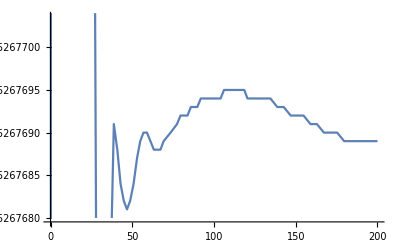

```mathematica
Plot[N1[t]/.sol,{t,0,200}]
```

```mathematica
N1ValFinal=(N1[tEnd]/.sol)/(N1Total/.NTotalVals)
N2ValFinal=(N2[tEnd]/.sol)/(N2Total/.NTotalVals)
```

{0.910775}

{0.999021}

```mathematica
CrpList = {1};
listN1Final = {};
listN2Final = {};
Do[
CrpTotalVal = {CrpTotal-> CrpVal};
tEnd = 10000;
sol = NDSolve[Flatten[Join[MBst/.kVals/.KdVals/.NTotalVals/.CrpTotalVal,concInit]],{N1,N2},{t,10000}];
N1ValFinal=(N1[tEnd]/.sol)/(N1Total/.NTotalVals);
N2ValFinal=(N2[tEnd]/.sol)/(N2Total/.NTotalVals);
listN1Final = Flatten[Append[listN1Final,N1ValFinal]];
listN2Final = Flatten[Append[listN2Final,N2ValFinal]];
,{CrpVal,CrpList}]
```

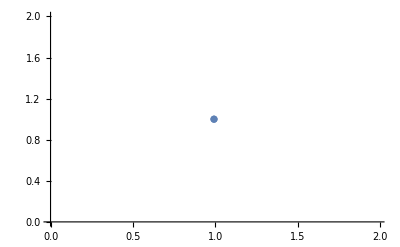

```mathematica
data=Transpose@{listN1Final,listN2Final};
ListPlot[data]
```